```mathematica
f[x_]:= Piecewise[{{-1, -π<x<0},{1,0<x<π}}]
```

```mathematica
a0= 1/(2*π)∫_-π^π (f[x])ⅆx
```

0

```mathematica
a0[f[x]]
```

0[Piecewise[{{-1, -π<x<0}, {1, 0<x<π}, {0, True}}]]

```mathematica
a[n_]=1/π∫_-π^π (f[x]*Cos[n*x])ⅆx
```

0

```mathematica
b[n_]=1/π∫_-π^π (f[x]*Sin[n*x])ⅆx
```

```mathematica
a[0]
```

0

```mathematica
a[1]
```

0

```mathematica
a[2]
```

0

```mathematica
a[3]
```

0

```mathematica
b[1]
```

4/π

```mathematica
b[2]
```

0

```mathematica
b[5]
```

4/(5 π)

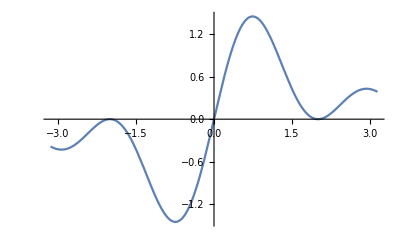

```mathematica
Plot[b[x], {x,-π,π}]
```

```mathematica
g[x_]:= b[1]Sin[x]+b[3]Sin[3*x]+b[5]Sin[5*x]+b[7]Sin[7*x]+b[9]Sin[9*x]+b[11]Sin[11*x]+b[13]Sin[13*x]
```

```mathematica
g[x]
```

(4 Sin[x])/π+(4 Sin[3 x])/(3 π)+(4 Sin[5 x])/(5 π)+(4 Sin[7 x])/(7 π)+(4 Sin[9 x])/(9 π)+(4 Sin[11 x])/(11 π)+(4 Sin[13 x])/(13 π)

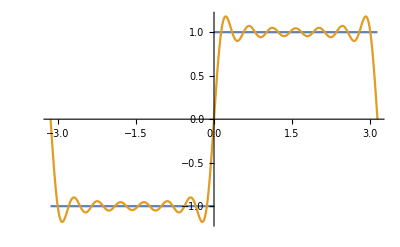

```mathematica
Plot[{f[x],g[x]},{x,-π,π}]
```

```mathematica
f2[x_]=Abs[x]
```

Abs[x]

```mathematica
aa= 1/(2*π)∫_-π^π (f2[x])ⅆx
```

π/2

```mathematica
aaa[n_]=1/π∫_-π^π (f2[x]*Cos[n*x])ⅆx
```

(2 (-1+Cos[n π]+n π Sin[n π]))/(n^2 π)

```mathematica
bb[n_]=1/π∫_-π^π (f2[x]*Sin[n*x])ⅆx
```

0

```mathematica
d:=aa+∑_(n=1)^3 (aaa[n]Cos[n*x]+bb[n]Sin[n*x])
```

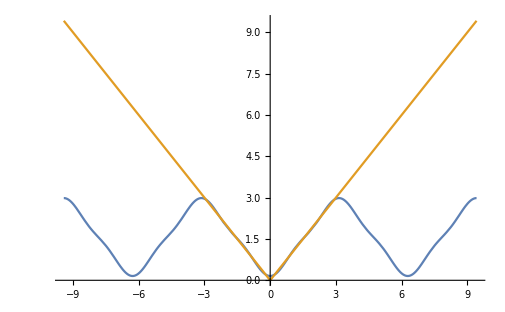

```mathematica
Plot[{d,f2[x]}, {x,-3π,3π}]
```

```mathematica
f3[x_]= Piecewise[{{-x+π, 0<x<π},{-x-π,-π<x<0}}]
```

Piecewise[{{π-x, 0<x<π}, {-π-x, -π<x<0}, {0, True}}]

```mathematica
a03= 1/(2*π)∫_-π^π (f3[x])ⅆx
```

0

```mathematica
a3[n_]=1/π∫_-π^π (f3[x]*Cos[n*x])ⅆx
```

0

```mathematica
b3[n_]=1/π∫_-π^π (f3[x]*Sin[n*x])ⅆx
```

(2 (n π-Sin[n π]))/(n^2 π)

```mathematica
d3=a03+∑_(n=1)^20 (a3[n]Cos[n*x]+b3[n]Sin[n*x])
```

2 Sin[x]+Sin[2 x]+2/3 Sin[3 x]+1/2 Sin[4 x]+2/5 Sin[5 x]+1/3 Sin[6 x]+2/7 Sin[7 x]+1/4 Sin[8 x]+2/9 Sin[9 x]+1/5 Sin[10 x]+2/11 Sin[11 x]+1/6 Sin[12 x]+2/13 Sin[13 x]+1/7 Sin[14 x]+2/15 Sin[15 x]+1/8 Sin[16 x]+2/17 Sin[17 x]+1/9 Sin[18 x]+2/19 Sin[19 x]+1/10 Sin[20 x]

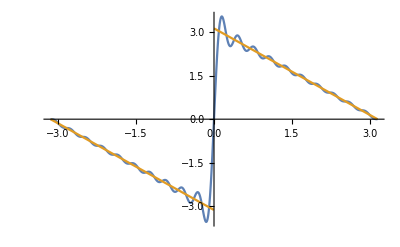

```mathematica
Plot[{d3,f3[x]}, {x,-π,π}]
```